```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\2d_toolbox.wl"]
```

### If we are working with a triangular lattice, there are one of two possible next two points based on the current given rod lengths

```mathematica
coord1 = {0,0};coord2={1,0};
length1 = 1;
length2 = 1.2;
coord3 = ThirdCoord[coord1,coord2,length1,length2]
```

{0.28,0.96}

#### Plotting one of the possible resulting triangular components

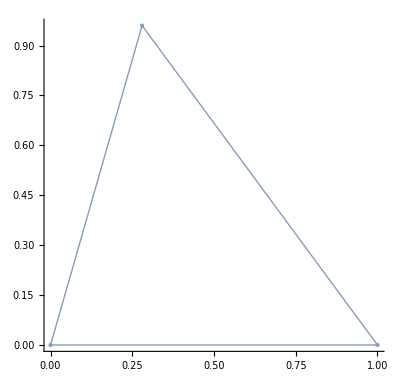

```mathematica
MeshTriag[coord1,coord2,coord3,Automatic]
```

#### Combining a few triangular building blocks with random module lengths between 0.6 and 1.0

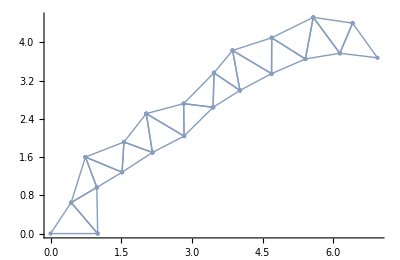

```mathematica
nfreepoints =20;
fixed1 = {0,0};
fixed2 = {1,0};
lens = RandomReal[{0.6,1},nfreepoints*2];
triagworm = MakeTriangleWorm[fixed1,fixed2,lens];

MeshAllTriag[triagworm,Automatic]
```

### The inverse problem: What should the module lengths be to move the mechanism in a certain way?

Define a structure and find the coordinates of the nodes in terms of the module lengths

```mathematica
nfreepoints = 5;
nunknowns = nfreepoints*2;
lattice =MakeSymbolicTriangleWorm[fixed1,fixed2,nfreepoints];
endeffector = lattice[[-1]];
```

The y-coordinate for the final point in the lattice as a function of the module lengths is for instance given as

```mathematica
Style[endeffector[[2]],Small]
```

len1 √(1-((1+len1^2-len2^2)^2)/(4 len1^2))+len5 Sin[1]+len9 Sin[ArcCos[(-len10^2+len9^2+(1/2 (1)+1-len7 1)^2+len7^2 Sin[ArcCos[1/1]+ArcTan[1]]^2)/(2 len9 √((1/2 (1+len1^2-len2^2)+1/2 (1)-len7 Cos[1])^2+len7^2 Sin[ArcCos[1]+1]^2))]+ArcTan[1/2 (1+len1^2-len2^2)+1/2 (1)+len7 Cos[ArcCos[1/(2 len7 √1)]+ArcTan[1,1]],1]]
 |  |  |  |

We now impose the constraint that the final point in the lattice should lay on a certain specified coordinate

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{len1→0.980243,len2→1.09127,len3→0.931496,len4→1.12499,len5→1.06206,len6→1.06673,len7→0.939417,len8→1.05861,len9→1.12598,len10→1.05918}

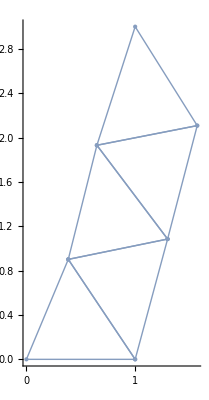

```mathematica
desired = {1,3};
endeffectorconstraints:= {Norm[endeffector-desired]};
constraints = Join[endeffectorconstraints];
sol = OptForDesired[constraints,MakeOptStartPoint[nunknowns]]
MeshAllTriag[lattice/.sol,Automatic]
```

Notice that in the previous example the modules could take any arbitrary length. Now imposing a constraint on the allowable lengths:

{0.6<len1<1,0.6<len2<1,0.6<len3<1,0.6<len4<1,0.6<len5<1,0.6<len6<1,0.6<len7<1,0.6<len8<1,0.6<len9<1,0.6<len10<1}

Optimisation Unsuccessfull, cost=0.191768

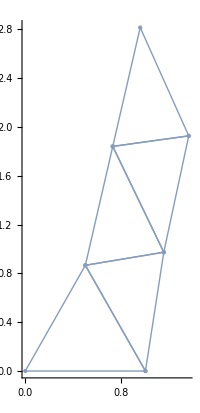

```mathematica
desired = {1,3};
endeffectorconstraints:= {Norm[endeffector-desired]};
modulelengthconstraint=MakeLengthConstraints[nunknowns,0.6,1]

constraints = Join[endeffectorconstraints,modulelengthconstraint];
sol = OptForDesired[constraints,MakeOptStartPoint[nunknowns]];
MeshAllTriag[lattice/.sol,Automatic]
```

In the above example the desired location could not be reached due to the length constraints.

#### Solving for a continuous path

```mathematica
path = Table[{i,2.0+ 0.3*Sin[15*i]},{i,0,1.2,0.01}];

optfordes = OptForDesired[constraints,MakeOptStartPoint[nunknowns]];

requiredlens = {optfordes};
Do[
endeffectorconstraints:= {Norm[endeffector-path[[j]]]};
modulelengthconstraint=MakeLengthConstraints[nunknowns,0.6,1];
constraints = Join[endeffectorconstraints,modulelengthconstraint];
optfordes =OptForDesired[constraints,SolAsStartPoint[optfordes]];
 AppendTo[requiredlens,optfordes],
{j,Length[path]-1}];
requiredlens;
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

```mathematica
Animate[MeshAllTriag[lattice/.requiredlens[[i]],{{0,2},{0,3}}],{i,Range[Length[path]-20]}]
```